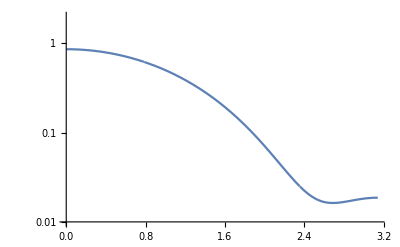

```mathematica
(*ai = {0.04642857142857134,0.28193161347707169,0.29326990129520958,-0.057446590093790564,0.13392857142857145,-0.068209261325097983};*) (* 4 freqs, start at 0 or 4/length *)
(*ai = {0.0080293409204241703,0.31172073473056788,0.39065184990291019,-0.089503246489572738,0.18175060217641945,-0.10314715573950872};*) (* 16 freqs, start at 4/length *)
ai = {0.012265853319319746,0.30985911754140028,0.23096773195702891,-0.02081962831047637,0.14574024678577233,-0.087323409631579849}; (* 16 freqs, cutoff starts at 0 *)
a0 = ai[[1]];
a1 = ai[[2]];
a2 = ai[[3]];
a3 = ai[[4]];
a4 = ai[[5]];
a5 = ai[[6]];
c =1.0;
h = {a4 + a5*c,a2 + a3*c, a0+a1*c, a2+a3*c, a4 + a5*c};
h3 = {1, 0, 0, 0};
LogPlot[Abs[ListFourierSequenceTransform[h, x]], {x, 0, Pi}, PlotRange->{10^-2, 2}]
```

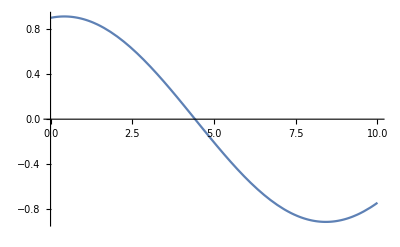

```mathematica
w = Pi/8;
Plot[h[[1]]*Cos[w*x] +h[[2]]*Cos[w (x-1)] +  h[[3]]*Cos[w(x-2)] + h[[4]]*Cos[w (x-3)], {x, 0, 10}]
```